# C. Sun Energy

```mathematica
(*Independent of θf, variable changed for Eγ*)
```

## Constants and Parameters (150MeV 0.5% bw)

```mathematica
(*Constants*)
re=2.8179403262*10^-15;
clight=299792458;
hbar=1.0545718*10^-34;
me=0.511*10^6; (*mc^2 really*)
elecharge=1.60217662*10^-19;
```

```mathematica
(*Parameters*)
Ee=150*10^6;
Q=32*10^-12;
Epulse=62*10^-6;
λ=1064*10^-9;
θcol=0.435*10^-3;(*0.435*10^-3*)
ϕ=0;
ϵnx=0.3*10^-6;
βx=0.126976;
σL=25*10^-6;
ΔEe=5*10^-4; (*relative energy spread*)
L=10; (*ICS source to collimator distance*)
```

## Observation Angle

```mathematica
θob[θx_,yc_,L_]:=Sqrt[θx^2+(yc/L)^2];
```

## SPE Intermediaries

```mathematica
(*Intermediary calculations for the scattered photon energy*)
γ[Ee_]:=Ee/me;
β[Ee_]:=Sqrt[1-1/γ[Ee]^2];
EL[λ_]:=(2*π*hbar*clight)/(λ*elecharge); (*in eV, using hbar*)
```

## Scattered Photon Energy Calc

```mathematica
Eγset[λ_,Ee_,ϕ_,θobs_]:=(EL[λ]*(1-β[Ee]*Cos[π-ϕ]))/(1-β[Ee]*Cos[θobs]+EL[λ]/Ee*(1-Cos[π-ϕ-θobs]));
```

## CSUN Preliminaries + Collimation

```mathematica
(*Preliminaries*)
Ne[Q_]:=Q/elecharge;
NL[Epulse_,λ_]:=Epulse/(EL[λ]*elecharge);
ϵx[Ee_,ϵnx_]:=ϵnx/γ[Ee];
k[λ_]:=EL[λ]/(hbar*clight);
zr[λ_,σL_]:=(π*σL^2)/λ;
σe[ΔEe_,Ee_]:=ΔEe*Ee; (*Conversion from relative*)
```

```mathematica
(*Collimation*)
R[L_,θcol_]:=L*θcol;
x0[L_,θcol_]:=R[L,θcol]; (*Condition for circular collimator*) 
y0[L_,θcol_]:=R[L,θcol];
```

## CSUN Intermediaries

```mathematica
a[λ_]:=EL[λ]/me;
γbar[λ_,Eγ_,θx_,yc_,L_]:=(2*Eγ*a[λ])/(4*EL[λ]-Eγ*θob[θx,yc,L]^2)*(1+Sqrt[1+(4*EL[λ]-Eγ*θob[θx,yc,L]^2)/(4*a[λ]^2*Eγ)]);
ξx[βx_,L_,λ_,Ee_,ϵnx_,σL_]:=1+(βx/L)^2+(2*k[λ]*βx*ϵx[Ee,ϵnx])/zr[λ,σL];
ζx[λ_,βx_,Ee_,ϵnx_,σL_]:=1+(2*k[λ]*βx*ϵx[Ee,ϵnx])/zr[λ,σL];
σθx[Ee_,ϵnx_,βx_,L_,λ_,σL_]:=Sqrt[(ϵx[Ee,ϵnx]*ξx[βx,L,λ,Ee,ϵnx,σL])/(βx*ζx[λ,βx,Ee,ϵnx,σL])];
σγ[ΔEe_,Ee_]:=σe[ΔEe,Ee]/me;
θxmax[λ_,Eγ_,yc_,L_]:=Sqrt[(4*EL[λ])/Eγ-(yc/L)^2];
```

## Prefactor

```mathematica
(*Prefactor*)
prefactor[L_,Q_,Epulse_,λ_,σL_,βx_,Ee_,ϵnx_,ΔEe_]:=(re^2*L^2*Ne[Q]*NL[Epulse,λ])/(2*π^2*hbar*clight*zr[λ,σL]*Sqrt[ζx[λ,βx,Ee,ϵnx,σL]]*σγ[ΔEe,Ee]*σθx[Ee,ϵnx,βx,L,λ,σL]);
prefactor[L,Q,Epulse,λ,σL,βx,Ee,ϵnx,ΔEe]
```

1.52552×10^18

## Separated Integral Terms

```mathematica
(*Separated Integral Terms, Each is calculated for the maximum scattered energy value, Plot of how each term looks 0 to θcol*)
```

```mathematica
(*Term 1*)
term1[λ_,Eγ_,θx_,yc_,L_]:=γbar[λ,Eγ,θx,yc,L]/(1+2*γbar[λ,Eγ,θx,yc,L]*a[λ]);
INTterm1[λ_,Eγ_,L_]:=NIntegrate[term1[λ,Eγ,θx,yc,L],{yc,-y0[L,θcol],y0[L,θcol]},{xc,-x0[L,θcol],x0[L,θcol]},{θx,-θxmax[λ,Eγ,yc,L],θxmax[λ,Eγ,yc,L]}];
```

```mathematica
Term1dat=Table[{Eγ,INTterm1[λ,Eγ,L]},{Eγ,Eγset[λ,Ee,ϕ,θcol],Eγset[λ,Ee,ϕ,0],10}];
```

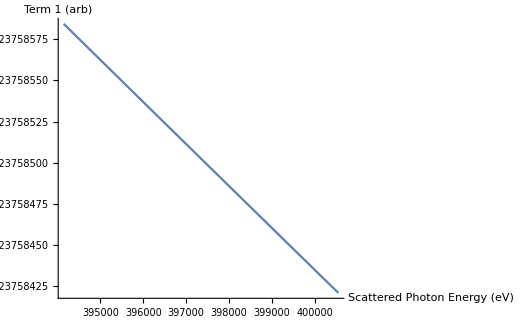

```mathematica
ListLinePlot[Term1dat,AxesLabel->{"Scattered Photon Energy (eV)","Term 1 (arb)"}]
```

```mathematica
(*Term2*)
term2[λ_,Eγ_,θx_,yc_,L_]:=1/4*((4*γbar[λ,Eγ,θx,yc,L]^2*EL[λ])/(Eγ*(1+γbar[λ,Eγ,θx,yc,L]^2*θob[θx,yc,L]^2))+(Eγ*(1+γbar[λ,Eγ,θx,yc,L]^2*θob[θx,yc,L]^2))/(4*γbar[λ,Eγ,θx,yc,L]^2*EL[λ]));
INTterm2[λ_,Eγ_,L_]:=NIntegrate[term2[λ,Eγ,θx,yc,L],{yc,-y0[L,θcol],y0[L,θcol]},{xc,-x0[L,θcol],x0[L,θcol]},{θx,-θxmax[λ,Eγ,yc,L],θxmax[λ,Eγ,yc,L]}]
```

```mathematica
Term2dat=Table[{Eγ,INTterm2[λ,Eγ,L]},{Eγ,Eγset[λ,Ee,ϕ,θcol],Eγset[λ,Ee,ϕ,0],10}];
```

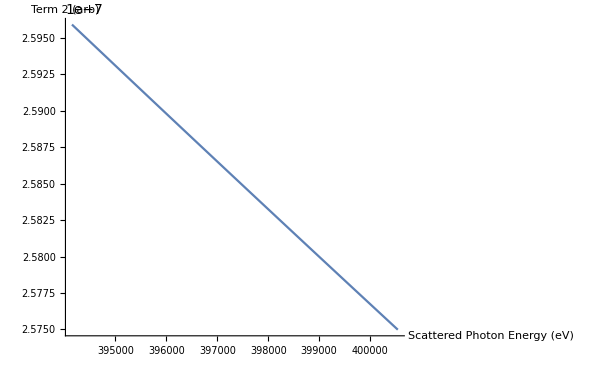

```mathematica
ListLinePlot[Term2dat,AxesLabel->{"Scattered Photon Energy (eV)","Term 2 (arb)"}]
```

```mathematica
(*Term3*)
term3[θx_,xc_,L_,Ee_,ϵnx_,βx_,λ_,σL_,yc_,ΔEe_,Eγ_]:=Exp[(-(θx-xc/L)^2)/(2*σθx[Ee,ϵnx,βx,L,λ,σL]^2)-(γbar[λ,Eγ,θx,yc,L]-γ[Ee])^2/(2*σγ[ΔEe,Ee]^2)];
INTterm3[L_,Ee_,ϵnx_,βx_,λ_,σL_,ΔEe_,Eγ_]:=NIntegrate[term3[θx,xc,L,Ee,ϵnx,βx,λ,σL,yc,ΔEe,Eγ],{yc,-y0[L,θcol],y0[L,θcol]},{xc,-x0[L,θcol],x0[L,θcol]},{θx,-θxmax[λ,Eγ,yc,L],θxmax[λ,Eγ,yc,L]}]
```

```mathematica
Term3dat=Table[{Eγ,INTterm3[L,Ee,ϵnx,βx,λ,σL,ΔEe,Eγ]},{Eγ,Eγset[λ,Ee,ϕ,θcol],Eγset[λ,Ee,ϕ,0],100}];
```

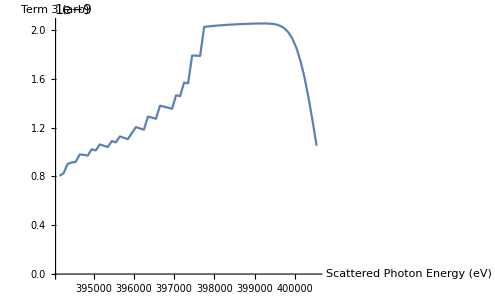

```mathematica
ListLinePlot[Term3dat,AxesLabel->{"Scattered Photon Energy (eV)","Term 3 (arb)"}]
```

## Integral Term

```mathematica
intterm[λ_,Ee_,θx_,yc_,L_,xc_,ϵnx_,βx_,σL_,ΔEe_,Eγ_]:=term1[λ,Eγ,θx,yc,L]*term2[λ,Eγ,θx,yc,L]*term3[θx,xc,L,Ee,ϵnx,βx,λ,σL,yc,ΔEe,Eγ];
INTterm[λ_,Ee_,L_,ϵnx_,βx_,σL_,ΔEe_,Eγ_]:=NIntegrate[intterm[λ,Ee,θx,yc,L,xc,ϵnx,βx,σL,ΔEe,Eγ],{yc,-y0[L,θcol],y0[L,θcol]},{xc,-x0[L,θcol],x0[L,θcol]},{θx,-θxmax[λ,Eγ,yc,L],θxmax[λ,Eγ,yc,L]}];
```

```mathematica
Intdat=Table[{Eγ,INTterm[λ,Ee,L,ϵnx,βx,σL,ΔEe,Eγ]},{Eγ,Eγset[λ,Ee,ϕ,θcol],Eγset[λ,Ee,ϕ,0],100}];
```

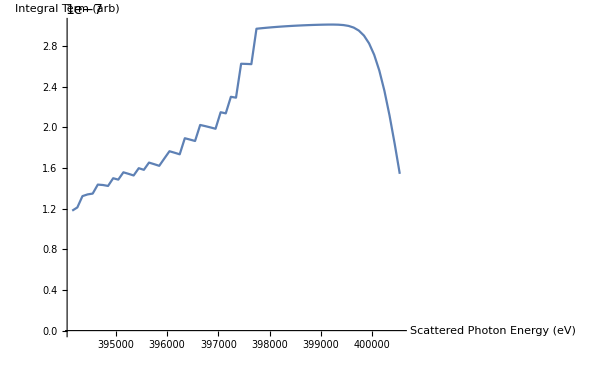

```mathematica
ListLinePlot[Intdat,AxesLabel->{"Scattered Photon Energy (eV)","Integral Term (arb)"}]
```

## C. Sun Calculation

```mathematica
(*Full Calc + Evaluation*)
dNγdEγ[L_,Q_,Epulse_,λ_,σL_,βx_,Ee_,ϵnx_,ΔEe_,Eγ_]:=prefactor[L,Q,Epulse,λ,σL,βx,Ee,ϵnx,ΔEe]*INTterm[λ,Ee,L,ϵnx,βx,σL,ΔEe,Eγ];
```

```mathematica
SpecDen=Table[{Eγ,dNγdEγ[L,Q,Epulse,λ,σL,βx,Ee,ϵnx,ΔEe,Eγ]},{Eγ,Eγset[λ,Ee,ϕ,θcol],Eγset[λ,Ee,ϕ,0],100}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

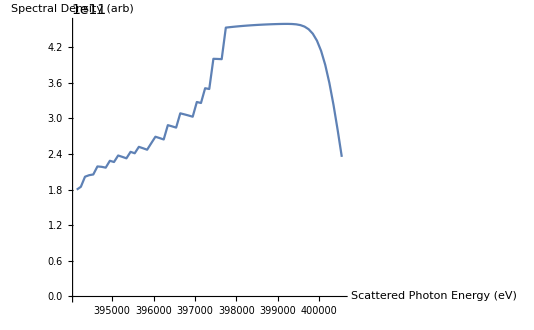

```mathematica
ListLinePlot[SpecDen,AxesLabel->{"Scattered Photon Energy (eV)","Spectral Density (arb)"}]
```